```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* Declare TDOS function that take the eigenvalue list and Gaussian width as inputs and returns TDOS as a function of energy *)
TDOS[Energy_,Eigenvalues_,Gwidth_]:=Apply[Plus,1/(Sqrt[2Pi]Gwidth)Exp[-(Energy-Eigenvalues)^2/(2 Gwidth^2)]];
```

```mathematica
(* Read orbital eigenvalues, in this example MOs.txt have three columns. If it contains more or less columns, change the size of the array in the second argument *)
Data1=ReadList["/home/zhenzhe/Desktop/mols_MOs/Azulene_MOs.txt",{Number,Number,Number,String}];
Data2=ReadList["/home/zhenzhe/Desktop/mols_MOs/Naphthalene_MOs.txt",{Number,Number,Number,String}];
(* Use the second column *)
(*Data1*)
OrbitalEnergies=Data1[[All,3]];
OrbitalEnergies2=Data2[[All,3]];
(*OrbitalEnergiesz*)
Length[OrbitalEnergies]
Length[OrbitalEnergies2]
OrbitalEnergies=OrbitalEnergies*27.2114
OrbitalEnergies2=OrbitalEnergies2*27.2114
```

273

274

{662.599,661.574,661.121,659.106,658.638,656.527,656.341,651.953,651.718,643.883,135.221,130.456,122.219,118.116,115.02,113.855,113.456,111.228,110.956,103.662,101.764,99.0495,98.268,97.9662,96.7814,96.6802,94.6701,92.6178,92.5609,92.5027,91.6866,89.7769,87.8253,87.034,85.3077,85.0803,83.9608,82.9205,81.3678,80.3316,79.8674,79.4905,78.5677,78.497,78.1868,78.1498,77.2053,76.9389,76.7887,76.7038,76.5631,76.3585,75.9269,75.4667,74.5786,74.5043,74.4773,73.8604,71.5845,71.3426,70.7494,70.4367,69.4157,68.7452,68.6652,68.3539,65.0537,64.4946,63.7386,63.0537,62.4896,60.9454,60.4118,60.0496,57.5861,57.514,57.4699,56.9676,56.2525,56.1842,55.6375,55.2217,55.0391,54.8851,54.5931,54.041,53.3528,52.5433,51.8712,51.297,51.2105,49.9438,49.842,49.6159,49.4529,49.0211,48.3876,48.2815,47.418,46.8534,46.1655,45.6343,45.6207,45.2226,44.5353,44.5026,43.9954,43.5551,43.5015,42.5178,41.5643,41.5573,38.6383,35.6902,34.8344,34.0396,33.6336,33.3614,33.1157,32.7399,32.2994,31.4762,30.7135,30.6139,30.5984,30.0629,29.5633,29.1244,29.0694,27.852,27.745,27.572,27.5118,27.3747,27.1967,26.0827,26.0408,25.7529,25.6533,25.007,24.7431,24.5858,23.6848,23.5438,23.0777,22.8883,22.8848,22.4078,22.0731,21.8464,21.5661,21.4635,20.7321,19.7606,19.423,19.39,19.2502,18.657,18.454,18.2235,18.0485,18.0373,17.6784,17.6401,17.5217,17.4455,17.2319,16.892,16.8735,16.1853,16.1023,15.1274,14.5333,13.9546,13.9186,13.0873,12.6408,11.5099,11.0568,10.9025,10.7477,10.4103,10.2005,10.0184,9.97706,9.69842,9.54086,9.3112,8.9501,8.90275,8.69595,8.56424,8.46193,8.1626,8.106,7.91743,7.89838,7.39878,7.25429,7.0834,7.04666,6.76149,6.52448,6.49999,6.45373,6.40475,6.25155,5.91984,5.90841,5.81997,5.56255,5.23085,4.95574,4.93914,4.92227,4.83547,4.69941,4.63329,4.59492,4.43437,4.24552,4.23301,4.09695,4.05096,3.71218,3.59816,3.40551,3.25285,3.07053,2.88495,2.38562,2.2697,1.74235,1.69962,1.34016,1.26587,1.02886,0.334428,-0.536881,-7.32585,-8.39036,-10.6233,-11.3842,-11.5425,-12.1156,-12.542,-12.5869,-13.1216,-13.2256,-13.5564,-14.8498,-14.8931,-16.0545,-16.6286,-17.5459,-17.6716,-19.556,-20.3854,-21.9944,-22.9449,-24.3841,-25.3942,-26.7983,-279.52,-279.522,-279.883,-280.256,-280.264,-280.296,-280.297,-280.597,-280.66,-280.662}

{662.377,662.305,660.672,660.505,657.423,656.14,655.533,654.669,651.486,643.78,134.653,134.006,121.822,117.219,116.384,113.339,112.779,112.598,112.596,104.598,102.556,102.067,99.9706,98.7034,98.5172,97.5689,95.5536,95.0459,93.9672,93.4118,90.5214,90.0564,87.1709,86.3644,84.4726,83.3164,82.4231,81.9305,81.792,81.1131,80.088,79.7452,79.5542,78.6684,78.4532,78.0418,77.6456,77.4845,77.3019,76.8208,76.8039,76.3821,76.2259,76.2254,76.0727,75.2047,74.904,74.901,72.3984,70.9701,70.905,69.8919,69.8726,68.9202,68.4974,68.2497,67.3874,63.7272,63.2222,62.3391,62.2164,60.3884,60.2596,60.2528,59.2487,57.7763,56.8101,56.1649,55.9455,55.9202,55.7581,55.1635,54.9561,54.7472,54.5232,54.2476,54.1104,53.6791,52.4682,52.272,50.4592,50.3041,49.9996,49.7367,49.6096,49.5541,48.2129,47.4161,47.1228,47.1095,45.8373,45.8278,45.5151,45.0226,44.8855,43.8025,43.5921,43.3641,43.0512,42.9524,42.9494,42.1341,39.2258,38.866,38.5036,34.3971,33.8575,33.5261,32.8793,32.3122,32.2014,31.6719,31.1913,31.1396,30.876,30.2438,29.3758,29.1739,28.7907,27.7978,27.733,27.689,27.4824,27.2835,26.7736,26.5262,26.3512,26.0097,25.9567,25.0467,25.0277,24.5828,24.4271,24.0652,23.7175,22.9463,22.6083,22.2366,22.1721,22.1242,21.8584,21.1063,20.417,20.3552,19.5908,19.2698,19.2129,18.9364,18.6727,18.2812,18.2344,18.0684,17.9481,17.6297,17.4893,17.3677,17.2542,17.2455,16.8654,16.5029,16.3685,15.7475,15.4566,15.2392,13.1243,12.5409,12.3216,11.7265,11.6895,10.8554,10.8481,10.5722,10.1779,9.95284,9.93488,9.78413,9.63175,9.47202,9.17133,9.16834,9.10521,9.00017,8.6037,8.27934,8.27852,8.04723,7.95988,7.93947,7.92668,7.50273,7.35252,7.06462,7.01347,6.98245,6.53155,6.17481,6.07032,6.03685,5.97562,5.84338,5.56555,5.41344,5.08772,5.04418,4.96227,4.88608,4.85805,4.85098,4.7424,4.49668,4.41015,4.18402,4.15845,4.06838,4.01504,3.76987,3.39571,3.19217,3.18292,3.05257,2.38018,2.27868,2.06616,1.735,1.70479,1.30016,1.28002,1.20302,1.07839,0.444634,-8.01893,-8.79472,-10.1441,-11.318,-11.4555,-11.5384,-12.4103,-13.3015,-13.3344,-13.8082,-13.8087,-14.5301,-14.6863,-16.0474,-16.4504,-16.6507,-18.9497,-19.3612,-19.7402,-22.4246,-23.0282,-23.9406,-25.3022,-26.7877,-280.043,-280.044,-280.053,-280.054,-280.07,-280.071,-280.073,-280.073,-280.292,-280.305}

```mathematica
GaussWidth=0.2;
TDOS1=TDOS[Ex,OrbitalEnergies,GaussWidth];
(* TDOS1 is now a smooth function of Ex *)

TDOS2=TDOS[Ex,OrbitalEnergies2,GaussWidth];
```

General::munfl: Exp[-5.82425×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.80678×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.79907×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

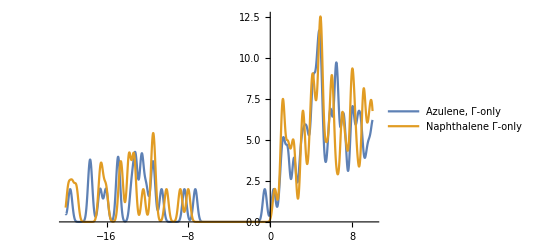

```mathematica
(* Plot two DOS functions. They are the same in this example *)
Emin=-20;
Emax=10;
Plot1=Plot[{TDOS1,TDOS2},{Ex,Emin,Emax},PlotRange->All,PlotLegends->{"Azulene, Γ-only","Naphthalene Γ-only"}]
```